# 3) Bang Bang Solution

Comprobando que Q(t) es correcta

```mathematica
DSolve[Q'[t]==A Exp[β t]-ν Q[t],Q,t]
```

{{Q→Function[{t},(A ⅇ^(-t ν+t (β+ν)))/(β+ν)+ⅇ^(-t ν) C[1]]}}

-t ν + t (β + ν)
                     A E                   C[1]
{{Q -> Function[{t}, ------------------- + ----]}}
                            β + ν           t ν
                                           E

Definiendo los valores

```mathematica
R=50
```

50

```mathematica
μ=0.022
```

0.022

```mathematica
b=0.0013
```

0.0013

```mathematica
c=1
```

1

```mathematica
ν=0.005
```

0.005

```mathematica
u0=0
```

0

```mathematica
u1=0.9999
```

0.9999

#### Definiendo Q

```mathematica
ecuacionu0=(b c (1-u0) R)/(b R u0 - μ)(Exp[t(b R u0 - μ)]- Exp[ν t])
```

-2.95455 (ⅇ^(-0.022 t)-ⅇ^(0.005 t))

```mathematica
t=205
```

205

```mathematica
Clear[t]
```

```mathematica
ecuacionu1=(b c (1-u1) R)/(b R u1 - μ)(Exp[t(b R u1 - μ)]- Exp[ν t])
```

0.000151186 (-ⅇ^(0.005 t)+ⅇ^(0.0429935 t))

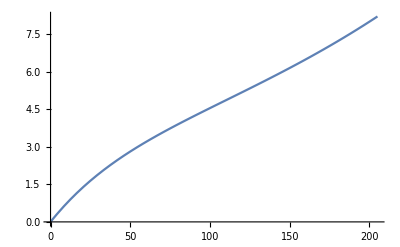

```mathematica
Plot[ecuacionu0,{t,0,205}]
```

```mathematica
Q0=Labeled[Plot[ecuacionu0,{t,0,205}],Style["Número de Abejas reinas en función del tiempo","Graphics"],Background->LightYellow]
```

-Graphics-Número de Abejas reinas en función del tiempo

```mathematica
Export["Qu0.png",Q0]
```

Qu0.png

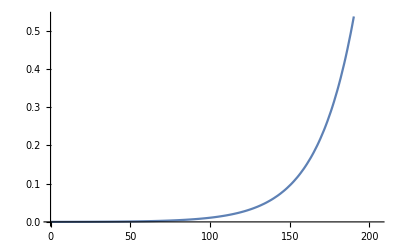

```mathematica
Plot[ecuacionu1,{t,0,205}]
```

```mathematica
Q1=Labeled[Plot[ecuacionu1,{t,0,205}],Style["Número de Abejas reinas en función del tiempo","Graphics"],Background->LightYellow]
```

-Graphics-Número de Abejas reinas en función del tiempo

```mathematica
Export["Qu1.png",Q1]
```

Qu1.png

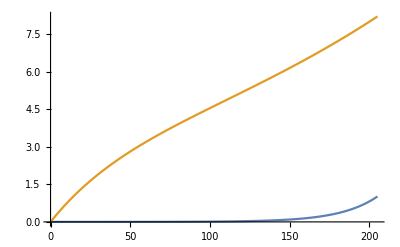

```mathematica
Plot[{ecuacionu1, ecuacionu0},{t,0,205}]
```

```mathematica
g[t_]:=If[t>260,ecuacionu0,ecuacionu1]
```

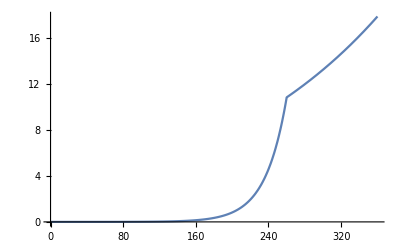

```mathematica
Plot[g[t],{t,0,360}]
```

#### Definiendo W

```mathematica
ecW0=Exp[t(b R u0 - μ)]
```

ⅇ^(-0.022 t)

```mathematica
ecW1=Exp[t(b R u1 - μ)]
```

ⅇ^(0.0429935 t)

```mathematica
0.0001*ecW0
```

0.0001 ⅇ^(-0.022 t)

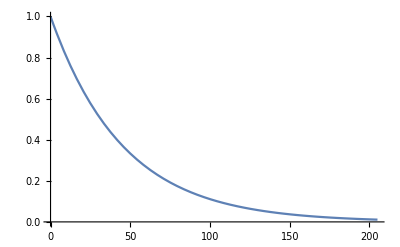

```mathematica
Plot[ecW0,{t,0,205}]
```

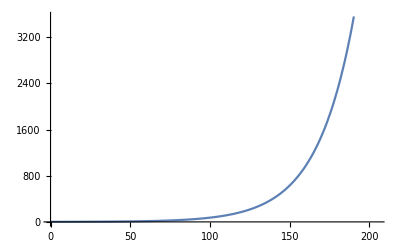

```mathematica
Plot[ecW1,{t,0,205}]
```

```mathematica
W0=Labeled[Plot[ecW0,{t,0,205}],Style["Número de Abejas obreras en función del tiempo","Graphics"],Background->LightYellow]
```

-Graphics-Número de Abejas obreras en función del tiempo

```mathematica
Export["Wu0.png",W0]
```

Wu0.png

```mathematica
W1=Labeled[Plot[ecW1,{t,0,205}],Style["Número de Abejas obreras en función del tiempo","Graphics"],Background->LightYellow]
```

-Graphics-Número de Abejas obreras en función del tiempo

```mathematica
Export["Wu1.png",W1]
```

Wu1.png

# 4)Cambiando valores de C en Q(t) con u=0

con c=1

```mathematica
c1=1
```

1

```mathematica
ecuacionu0c1=(b c1 (1-u0) R)/(b R u0 - μ)(Exp[t(b R u0 - μ)]- Exp[ν t])
```

-2.95455 (ⅇ^(-0.022 t)-ⅇ^(0.005 t))

```mathematica
Qc1=Labeled[Plot[ecuacionu0c1,{t,0,205}],Style["Número de Abejas reinas en función del tiempo, c=1","Graphics"],Background->LightYellow]
```

-Graphics-Número de Abejas reinas en función del tiempo, c=1

```mathematica
Export["Qc1.png",Qc1]
```

Qc1.png

c=2

```mathematica
c2=2
```

2

```mathematica
ecuacionu0c2=(b c2 (1-u0) R)/(b R u0 - μ)(Exp[t(b R u0 - μ)]- Exp[ν t])
```

-5.90909 (ⅇ^(-0.022 t)-ⅇ^(0.005 t))

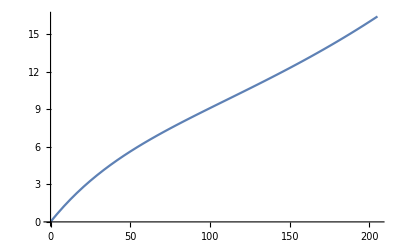
-Graphics-Número de Abejas reinas en función del tiempo, c=2

```mathematica
Qc2=Labeled[Plot[ecuacionu0c2,{t,0,205}],Style["Número de Abejas reinas en función del tiempo, c=2","Graphics"],Background->LightYellow]
```

```mathematica
Export["Qc2.png",Qc2]
```

Qc2.png

c=1/2

```mathematica
c12=1/2
```

1/2

```mathematica
ecuacionu0c12=(b c12 (1-u0) R)/(b R u0 - μ)(Exp[t(b R u0 - μ)]- Exp[ν t])
```

-1.47727 (ⅇ^(-0.022 t)-ⅇ^(0.005 t))

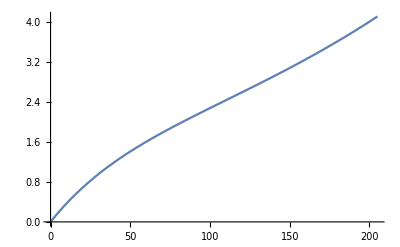
-Graphics-Número de Abejas reinas en función del tiempo, c=1/2

```mathematica
Qc12=Labeled[Plot[ecuacionu0c12,{t,0,205}],Style["Número de Abejas reinas en función del tiempo, c=1/2","Graphics"],Background->LightYellow]
```

```mathematica
Export["Qc12.png",Qc12]
```

Qc12.png

definiendo los valores

```mathematica
R=50
```

50

```mathematica
μ=0.022
```

0.022

```mathematica
b=0.0013
```

0.0013

```mathematica
c=1
```

1

```mathematica
ν=0.005
```

0.005

```mathematica
u0=0
```

0

```mathematica
ecuacionu0=(b c (1-u0) R)/(b R u0 - μ)(Exp[t(b R u0 - μ)]- Exp[ν t])
```

-2.95455 (ⅇ^(-0.022 t)-ⅇ^(0.005 t))

```mathematica
t=205
```

205

```mathematica
ecuacionu0
```

8.2021

# 5) Modelando las variaciones en las estaciones del año. Cambios en R(t)

```mathematica
Clear[t]
```

```mathematica
m=0.07
```

0.07

```mathematica
Rt=Exp[-t/ 20]
```

ⅇ^(-t/20)

```mathematica
c
```

1

```mathematica
u0
```

0

```mathematica
ecuacionu0R=(b c (1-u0) Rt)/(b R u0 - μ)(Exp[t(b R u0 - μ)]- Exp[ν t])
```

-0.0590909 ⅇ^(-t/20) (ⅇ^(-0.022 t)-ⅇ^(0.005 t))

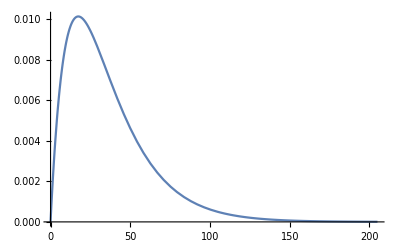
-Graphics-Número de Abejas obreras en función del tiempo, con R(t)

```mathematica
rt=Labeled[Plot[ecuacionu0R,{t,0,205}],Style["Número de Abejas obreras en función del tiempo, con R(t)","Graphics"],Background->LightYellow]
```

```mathematica
Export["Rt.png",rt]
```

Rt.png

# 6) Considerando el comportamiento de las reinas que abandonan la colmena a mitad de temporada

```mathematica
Clear[t]
```

```mathematica
m=0.07
```

0.07

```mathematica
Rt=Exp[-m t]
```

ⅇ^(-0.07 t)

```mathematica
R
```

50

```mathematica
Rt=205-(1t)
```

205-t

31 t

```mathematica
ecuacionu0R=(b c (1-u0) Rt)/(b R u0 - μ)(Exp[t(b R u0 - μ)]- Exp[ν t])
```

-1.83182 (ⅇ^(-0.022 t)-ⅇ^(0.005 t)) t

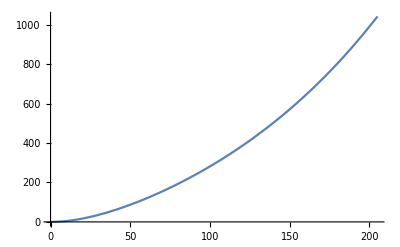
-Graphics-Número de Abejas obreras en función del tiempo, con R(t)=Exp[-t]

```mathematica
rt=Labeled[Plot[ecuacionu0R,{t,0,205}],Style["Número de Abejas obreras en función del tiempo, con R(t)=Exp[-t]","Graphics"],Background->LightYellow]
```